```mathematica
ϵ ={0.012,0.008,0.004,0,-0.004,-0.008,-0.012}
```

{0.012,0.008,0.004,0,-0.004,-0.008,-0.012}

```mathematica
ϵAve=(1/240000){-0.0036*79049-.0030*65498-0.002*25570-0.0017*16500-0.001*12478-0.0004*10878+0.00023*15122+0.00088*13128+0.001529*1422,0.0036*79049+0.003*65498+0.0023*25570+0.0017*16500+0.001*12478+0.0004*10878-0.0002*15122-0.0008*13128-0.0015*1422,0.0073*79049+0.006*65498+0.004*25570+0.0034*16500+0.0021*12478+0.0008*10878-0.0004*15122-0.0017*13128-0.003*1422,0.0109*79049+65498*0.009+25570*0.007+16500*0.0051+12478*0.003+10878*0.0012-15122*0.0007-13128*0.0026-1422*0.0045}
```

{-0.00233285,0.00237125,0.00471125,0.00714011}

```mathematica
Nx={31318+7968+2864+1225+936,11642+13022+7242+8561+9889+4711,15295+13549+3732+12205+11654+2497,68436+11815+4000+3263+1385+839,193943+25459}
```

{44311,55067,58932,89738,219402}

```mathematica
Ny={13066+4037+5798+2968,9558+9579+5213+10191+11965+6218,10105+10648+3052+15015+16571+4179,10816+2767+1591+15500+3061+1726}
```

{25869,52724,59570,35461}

```mathematica
Nz ={8248+6994+2293+10688+9364+2745+889+1177,5967+12773+7427+7384+17342+8514+1342+1795,1305+266+12228+9123+191+401+1861+19679+16249+4862,26582+2503}
```

{42398,62544,66165,29085}

```mathematica
dof = 1681043; ndofpercpu=10906;
```

```mathematica
Nx+Ny
```

{107791,118502,125199,219402}

```mathematica
Nz/240000.
```

{0.176658,0.2606,0.275688,0.121188}

```mathematica
(Nx+Ny)/240000.
```

{0.449129,0.493758,0.521663,0.914175}

T = 246 C for mine and 25 C for Chen

```mathematica
plotFont={FontWeight->"Bold",FontSize->12};
```

```mathematica
MyDataNc={{0,0},{0.00237125,0.27568},{0.004,0.2606},{0.007,0.17}};
```

```mathematica
ChenDataNc={{-0.012,1.0},{-0.008,-0.97},{-0.004,0.832},{-0.002,0.751},{0,0.646},{0.002,0.539},{0.006,0.261},{0.012,0}};
```

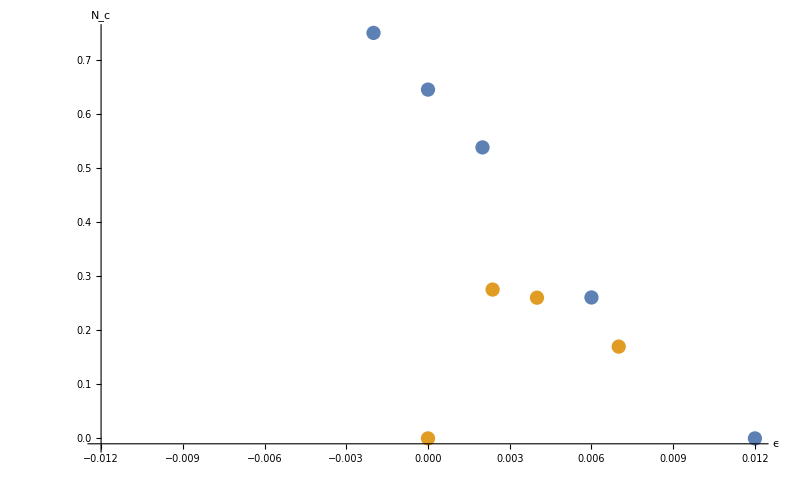

```mathematica
ListPlot[{ChenDataNc,MyDataNc},AxesOrigin->{-0.012,-0.01},AxesLabel->{"ϵ","N_c"},BaseStyle->plotFont]
```

## Strain coupling data from MOOSE -- FERRET:

```mathematica
ClearAll[Nz]
```

```mathematica
plotFont={FontWeight->"Bold",FontSize->12};
```

We consider a slab of dimensions 90 x 90 x 14 nm at T = 520 K with the substrate interface constant stress-free strain at the boundary ϵ^0. The only other boundary condition is that the bottom of the substrate is displacement free. The rest of the slab is allowed to relax due to the stress-divergence problem instananeously at each time step. This produces a inhomogenous distribution of strains within the slab. Chen’s group essentially did something similar but with slightly different elastic boundary conditions. They take the average strain ϵ of a 128 x 128 x 18 nm slab at T = 298 K and get the following data.

```mathematica
ChenDataNc={{-0.012,1.0},{-0.008,0.97},{-0.004,0.832},{-0.002,0.751},{0,0.646},{0.002,0.539},{0.006,0.261},{0.012,0}};
```

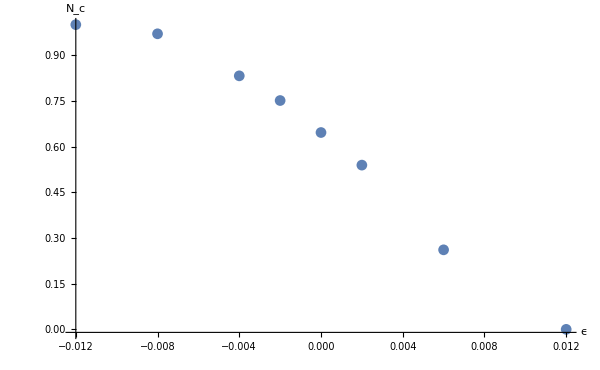

```mathematica
ListPlot[{ChenDataNc},AxesOrigin->{-0.012,-0.01},AxesLabel->{"ϵ","N_c"},BaseStyle->plotFont,ImageSize->600]
```

Although the temperatures are not the same, they should exhibit similar dependence.

```mathematica
ϵAve=Reverse[1/240000{0.01*79049+0.009*65498+0.007*25570+0.005*16500+0.003*12478+0.0012*10878-0.0007*15122-0.0026*13128-0.00458*1422,0.0073*79049+0.006*65498+0.0047*25570+0.0034*16500+0.0021*12478+0.00083*10878-0.00046*15122-0.0017*13128-0.003*1422,0.0036*79049+0.0030*65498+0.0023*25570+0.0017*16500+0.001*12478+0.0004*10878-0.0002*15122-0.00088*16128-0.0015*1422,-0.0036*79049-0.003*65498-0.0023*25570-0.0017*16500-0.001*12478-0.0004*10878+0.0002*15122+0.00088*13128+0.00152*1422,-0.0073*79049-0.006*65498-0.0047*25570-0.0034*16500-0.0021*12478-0.00083*10878+0.00046*15122+0.0017*13128+0.003*1422,-0.00683633*240000}]
```

{-0.00683633,-0.00478341,-0.00236676,0.00235588,0.00478341,0.00683633}

```mathematica
Nx0=Reverse[{29126+21344,31110+25302,82522+5094,40734+2455,35993+6063,36043+7795}]
```

{43838,42056,43189,87616,56412,50470}

```mathematica
Nx=Reverse[{11642+13022+7242+3590+8561+9889+4711+2429,15295+13549+3732+2108+12205+11654+2497+1613,68436+11815+4000+2863+3263+1385+839+675,31318+7968+2864+2095+1225+936+589+436,20982+13271+3088+1957+1723+3174+2280+1590,20756+13684+2801+1973+2097+4573+1965+1400}]
```

{49249,48065,47431,93276,62653,61086}

```mathematica
Ny0=Reverse[{22280+25952,22512+34110,14410+19489,18038+9480,20177+12311,21681+14155}]
```

{35836,32488,27518,33899,56622,48232}

```mathematica
Nx0+Ny0
```

{79674,74544,70707,121515,113034,98702}

```mathematica
Ny=Reverse[{9558+9579+5213+2742+10191+11965+6218+3038,10105+10648+3052+1915+15015+16571+4179+2518,10816+2767+1591+1363+1550+3061+1726+1296,13066+4037+1777+1358+5798+2968+1302+1023,9972+8612+2765+1737+5681+5413+2248+1583,9618+1031+2985+1751+6189+6620+2426+1540}]
```

{32160,38011,31329,24170,64003,58504}

```mathematica
(Nx+Ny)/240000.
```

{0.339204,0.35865,0.328167,0.489358,0.527733,0.498292}

```mathematica
Nz0=Reverse[{14842+19152,29724+1716+2253+23219,13656+14213+21738+22984,25884+5375+102499+6354,27553+92600+5807+5253,30764+5181+88162+6028}]
```

{130135,131213,140112,72591,56912,33994}

```mathematica
Nz = Reverse[{889+2293+8248+6994+4268+1177+2745+9364+10688+5094,1342+5967+12773+7427+4206+1795+7384+17342+8514+4986,1305+12228+9123+3624+1861+19679+16249+4862,13935+9610+3766+2305+88539+11759+3792+2557,3532+21989+3371+2098+52027+38808+3166+2225,2739+24773+4605+2079+18492+66900+4326+2449}]
```

{126363,127216,136263,68931,71736,51760}

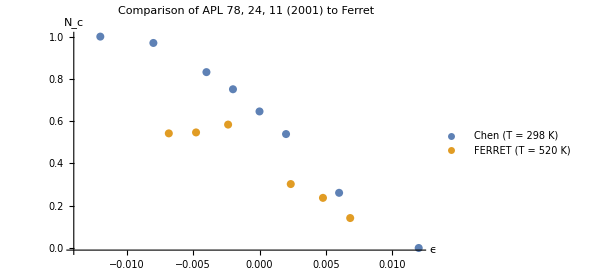

```mathematica
ListPlot[{ChenDataNc,Table[{ϵAve[[k]],Nz0[[k]]/240000},{k,1,Length[Nz0],1}]},PlotLegends->{"Chen (T = 298 K)","FERRET (T = 520 K)"},AxesOrigin->{-0.014,-0.01},AxesLabel->{"ϵ","N_c"},BaseStyle->plotFont,ImageSize->450,PlotLabel->"Comparison of APL 78, 24, 11 (2001) to Ferret"]
```

```mathematica
percChange=Reverse[{8.87*10^-5,9.94*10^-4,6.18*10^-4,1.0*10^-4,7.1*10^-5,5.7*10^-5}]
```

{0.000057,0.000071,0.0001,0.000618,0.000994,0.0000887}

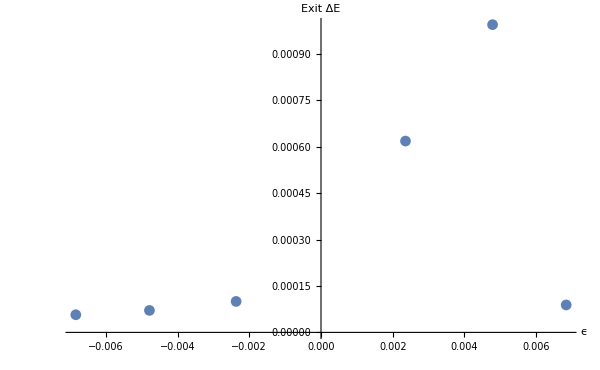

```mathematica
ListPlot[Table[{ϵAve[[k]],percChange[[k]]},{k,1,Length[percChange],1}],AxesLabel->{"ϵ","Exit ΔE"},BaseStyle->plotFont,ImageSize->600]
```